## Getting a0(Δ)

### Potential

```mathematica
g[k_]={{1/(1+k^2/β1^2),0},{0,1/(1+k^2/β2^2)}};
```

### Scattering Amplitude

```mathematica
G0[En_,H_]={{1/(En-H-ⅈ ϵ),0},{0,1/(En-H-δ^2/m-ⅈ ϵ)}};

λ={{λo,λx},{λx,λc}};
```

```mathematica
Jmat[En_]=Limit[Integrate[g[q].G0[En,q^2/m].g[q]*(4π q^2)/(2π)^3,{q,0,∞},Assumptions->{m>0,δ>0,En∈Reals,β1∈Reals,β2∈Reals,β1>0,β2>0,ϵ>0}],ϵ->0];
```

```mathematica
Δmat[En_]=IdentityMatrix[2]-λ.Jmat[En];

τ[En_]=Inverse[Δmat[En]].λ;
```

```mathematica
Fff[p_]=-m/(4π)g[p].τ[p^2/m].g[p]/.1/(√(-p^2))->1/(-ⅈ p)/.√(-p^2)->-ⅈ p;
```

```mathematica
f[p_]=Fff[p][[1,1]];
```

### Scattering Length

```mathematica
ERE[p_,δ_]=Series[1/f[p],{p,0,1}]+ⅈ p//Normal;
```

```mathematica
p0[δ_]=Simplify[Coefficient[ERE[p,δ],p,0]]/.√(δ^2)->δ
p1[δ_]=Simplify[Coefficient[ERE[p,δ],p,1]]/.√(δ^2)->δ
```

(-64 π^2 (β2^2+2 β2 δ+δ^2)-8 m π (β2^3 λc+β1 β2^2 λo+2 β1 β2 δ λo+β1 δ^2 λo)+m^2 β1 β2^3 (-λc λo+λx^2))/(2 m (8 π (β2^2+2 β2 δ+δ^2) λo+m β2^3 (λc λo-λx^2)))

0

```mathematica
a0[δ_]=Simplify[-1/p0[δ]]
```

(2 m (8 π (β2+δ)^2 λo+m β2^3 (λc λo-λx^2)))/(64 π^2 (β2+δ)^2+8 m π (β2^3 λc+β1 β2^2 λo+2 β1 β2 δ λo+β1 δ^2 λo)+m^2 β1 β2^3 (λc λo-λx^2))

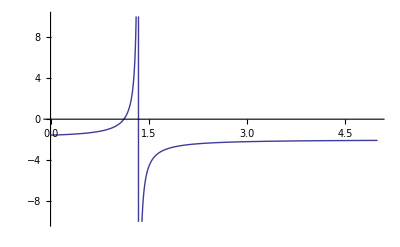

```mathematica
Plot[a0[δ]/.{λx->1,λo->-1,λc->-10,β1->1,β2->1,m->4π},{δ,0,5},PlotRange->{-10,10}]
```

```mathematica
δsoln1=Solve[Denominator[a0[δ]]==0,δ][[1]]
δsoln2=Solve[Denominator[a0[δ]]==0,δ][[2]]
```

{δ→(-32 π^2 β2-4 m π β1 β2 λo-√(2 π) √(-64 m π^2 β2^3 λc-16 m^2 π β1 β2^3 λc λo-m^3 β1^2 β2^3 λc λo^2+8 m^2 π β1 β2^3 λx^2+m^3 β1^2 β2^3 λo λx^2))/(4 π (8 π+m β1 λo))}

{δ→(-32 π^2 β2-4 m π β1 β2 λo+√(2 π) √(-64 m π^2 β2^3 λc-16 m^2 π β1 β2^3 λc λo-m^3 β1^2 β2^3 λc λo^2+8 m^2 π β1 β2^3 λx^2+m^3 β1^2 β2^3 λo λx^2))/(4 π (8 π+m β1 λo))}

```mathematica
Params={β1->0.241136476269006,m->4.00831299692006×10^8,β2->1.42270520998714,δ->4.80874849133680,λo->-2.025617195012436×10^-7,λx->1.132002120803345×10^-8,λc->-8.453468720889074×10^-7};
Det[τ[-γ^2/m]]/.Params/.{γ->0.09691389604637443}
```

1.46826+0. ⅈ

### Fortran

```mathematica
t11=τ[En][[1,1]]//Simplify;
t11/.{β1->b1,β2->b2,λo->cStr[1,1],λx->cStr[1,2],λc->cStr[2,2],En->cEtau,δ->Echan[2],m->mRb}//FortranForm
```

(8*(b1**2 + cEtau*mRb)**2*Pi**2*(8*cEtau*mRb*Pi*cStr(1,1) + b2**3*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2)) - 
     -      8*Pi*cStr(1,1)*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))))/
     -  (Pi*(64*cEtau**3*mRb**3*Pi**2 + 8*cEtau**2*mRb**2*Pi*
     -        (-(mRb*(b1**3*cStr(1,1) + b2**3*cStr(2,2))) + 
     -          8*Pi*(2*b1**2 - b2**2 - Echan(2)**2 - 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))) - 
     -       b1**4*(b1*b2**3*mRb**2*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2)) + 
     -          64*Pi**2*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)) + 
     -          8*mRb*Pi*(b1*b2**2*cStr(1,1) + b2**3*cStr(2,2) + b1*cStr(1,1)*Echan(2)**2 + 
     -             2*b1*b2*cStr(1,1)*Sqrt(-(cEtau*mRb) + Echan(2)**2))) + 
     -       b1**2*cEtau*mRb*(b1*b2**3*mRb**2*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2)) + 
     -          8*mRb*Pi*(b1*b2**2*cStr(1,1) - 2*b2**3*cStr(2,2) + b1*cStr(1,1)*(b1**2 + Echan(2)**2) + 
     -             2*b1*b2*cStr(1,1)*Sqrt(-(cEtau*mRb) + Echan(2)**2)) + 
     -          64*Pi**2*(b1**2 - 2*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))))) + 
     -    b1**4*mRb*Sqrt(cEtau*mRb)*(8*cEtau*mRb*Pi*cStr(1,1) + b2**3*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2)) - 
     -       8*Pi*cStr(1,1)*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))*Log(cEtau*mRb) + 
     -    2*b1**4*mRb*Sqrt(cEtau*mRb)*(8*cEtau*mRb*Pi*cStr(1,1) + b2**3*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2)) - 
     -       8*Pi*cStr(1,1)*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))*Log(-(1/Sqrt(cEtau*mRb))))

```mathematica
t12=τ[En][[1,2]]//Simplify;
t12/.{β1->b1,β2->b2,λo->cStr[1,1],λx->cStr[1,2],λc->cStr[2,2],En->cEtau,δ->Echan[2],m->mRb}//FortranForm
```

(64*(b1**2 + cEtau*mRb)**2*Pi**3*cStr(1,2)*(-b2**2 + cEtau*mRb - Echan(2)**2 - 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))/
     -  (Pi*(64*cEtau**3*mRb**3*Pi**2 + 8*cEtau**2*mRb**2*Pi*
     -        (-(mRb*(b1**3*cStr(1,1) + b2**3*cStr(2,2))) + 
     -          8*Pi*(2*b1**2 - b2**2 - Echan(2)**2 - 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))) - 
     -       b1**4*(b1*b2**3*mRb**2*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2)) + 
     -          64*Pi**2*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)) + 
     -          8*mRb*Pi*(b1*b2**2*cStr(1,1) + b2**3*cStr(2,2) + b1*cStr(1,1)*Echan(2)**2 + 
     -             2*b1*b2*cStr(1,1)*Sqrt(-(cEtau*mRb) + Echan(2)**2))) + 
     -       b1**2*cEtau*mRb*(b1*b2**3*mRb**2*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2)) + 
     -          8*mRb*Pi*(b1*b2**2*cStr(1,1) - 2*b2**3*cStr(2,2) + b1*cStr(1,1)*(b1**2 + Echan(2)**2) + 
     -             2*b1*b2*cStr(1,1)*Sqrt(-(cEtau*mRb) + Echan(2)**2)) + 
     -          64*Pi**2*(b1**2 - 2*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))))) + 
     -    b1**4*mRb*Sqrt(cEtau*mRb)*(8*cEtau*mRb*Pi*cStr(1,1) + b2**3*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2)) - 
     -       8*Pi*cStr(1,1)*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))*Log(cEtau*mRb) + 
     -    2*b1**4*mRb*Sqrt(cEtau*mRb)*(8*cEtau*mRb*Pi*cStr(1,1) + b2**3*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2)) - 
     -       8*Pi*cStr(1,1)*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))*Log(-(1/Sqrt(cEtau*mRb))))

```mathematica
t21=τ[En][[2,1]]//Simplify;
t21/.{β1->b1,β2->b2,λo->cStr[1,1],λx->cStr[1,2],λc->cStr[2,2],En->cEtau,δ->Echan[2],m->mRb}//FortranForm
```

(64*(b1**2 + cEtau*mRb)**2*Pi**3*cStr(1,2)*(-b2**2 + cEtau*mRb - Echan(2)**2 - 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))/
     -  (Pi*(64*cEtau**3*mRb**3*Pi**2 + 8*cEtau**2*mRb**2*Pi*
     -        (-(mRb*(b1**3*cStr(1,1) + b2**3*cStr(2,2))) + 
     -          8*Pi*(2*b1**2 - b2**2 - Echan(2)**2 - 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))) - 
     -       b1**4*(b1*b2**3*mRb**2*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2)) + 
     -          64*Pi**2*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)) + 
     -          8*mRb*Pi*(b1*b2**2*cStr(1,1) + b2**3*cStr(2,2) + b1*cStr(1,1)*Echan(2)**2 + 
     -             2*b1*b2*cStr(1,1)*Sqrt(-(cEtau*mRb) + Echan(2)**2))) + 
     -       b1**2*cEtau*mRb*(b1*b2**3*mRb**2*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2)) + 
     -          8*mRb*Pi*(b1*b2**2*cStr(1,1) - 2*b2**3*cStr(2,2) + b1*cStr(1,1)*(b1**2 + Echan(2)**2) + 
     -             2*b1*b2*cStr(1,1)*Sqrt(-(cEtau*mRb) + Echan(2)**2)) + 
     -          64*Pi**2*(b1**2 - 2*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))))) + 
     -    b1**4*mRb*Sqrt(cEtau*mRb)*(8*cEtau*mRb*Pi*cStr(1,1) + b2**3*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2)) - 
     -       8*Pi*cStr(1,1)*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))*Log(cEtau*mRb) + 
     -    2*b1**4*mRb*Sqrt(cEtau*mRb)*(8*cEtau*mRb*Pi*cStr(1,1) + b2**3*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2)) - 
     -       8*Pi*cStr(1,1)*(b2**2 + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2)))*Log(-(1/Sqrt(cEtau*mRb))))

```mathematica
t22=τ[En][[2,2]]//Simplify;
t22/.{β1->b1,β2->b2,λo->cStr[1,1],λx->cStr[1,2],λc->cStr[2,2],En->cEtau,δ->Echan[2],m->mRb}//FortranForm
```

(Pi*(8*cEtau**2*mRb**2*Pi*cStr(2,2) + b1**2*cEtau*mRb*(16*Pi*cStr(2,2) + b1*mRb*(cStr(1,2)**2 - cStr(1,1)*cStr(2,2))) + 
     -       b1**4*(8*Pi*cStr(2,2) + b1*mRb*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2)))) + 
     -    b1**4*mRb*Sqrt(cEtau*mRb)*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2))*Log(cEtau*mRb) + 
     -    2*b1**4*mRb*Sqrt(cEtau*mRb)*(-cStr(1,2)**2 + cStr(1,1)*cStr(2,2))*Log(-(1/Sqrt(cEtau*mRb))))/
     -  (8.*(b1**2 + cEtau*mRb)**2*Pi**2*((b1**3*b2**3*mRb**2*cStr(1,2)**2*
     -         (-(b1**2*Pi) + cEtau*mRb*Pi - b1*Sqrt(cEtau*mRb)*Log(cEtau*mRb) - 2*b1*Sqrt(cEtau*mRb)*Log(-(1/Sqrt(cEtau*mRb))))
     -         )/(64.*(b1**2 + cEtau*mRb)**2*Pi**3*(b2**2 - cEtau*mRb + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))) + 
     -      (1 + (b2**3*mRb*cStr(2,2))/(8.*Pi*(b2**2 - cEtau*mRb + Echan(2)**2 + 2*b2*Sqrt(-(cEtau*mRb) + Echan(2)**2))))*
     -       (1 - (b1**3*mRb*cStr(1,1)*(-(b1**2*Pi) + cEtau*mRb*Pi - b1*Sqrt(cEtau*mRb)*Log(cEtau*mRb) - 
     -              2*b1*Sqrt(cEtau*mRb)*Log(-(1/Sqrt(cEtau*mRb)))))/(8.*(b1**2 + cEtau*mRb)**2*Pi**2))))

## Looping through mag field

### Constants

```mathematica
ℏc=197.326968;
cLight=2.99792458*10^17;
ℏPlank=2 π ℏc/cLight;
μBohr=5.788381804*10^-5;
μe=1.0011596521859 μBohr;
aBohr=0.052917720859;

Ehf=3.036*10^9 ℏPlank;
Bhf=Ehf/μe 10^4;

mRb=84.911789738*931.494028*10^6;
```

### Hyperfine and Zeeman

```mathematica
Hhf[i_,s_,f_]:=(f (f+1)-i (i+1)-s (s+1))/(2 i+1);
Sz[i_,s_,finit_,m_,ffin_]:=Sqrt[3]/2 (-1)^(ffin+s+i+1) Sqrt[(2 s+1) (2 finit+1)]SixJSymbol[{i,s,finit},{1,ffin,s}]ClebschGordan[{finit,m},{1,0},{ffin,m}];
```

### Actual Loop

```mathematica
Clear[ScatList,δlist,δalist,δblist,δclist,δdlist];
ScatList={};
δlist={};
δalist={};
δblist={};
δclist={};
δdlist={};

Do[{

ρB=2*Bfield/Bhf;

(*Single Atom Stuff*)
H33=Hhf[5/2,1/2,3]+ρB*Sz[5/2,1/2,3,-3,3];
Hm3={{0,0},{0,H33}};
e3=Eigenvalues[Hm3];

H22=Hhf[5/2,1/2,2]+ρB*Sz[5/2,1/2,2,-2,2];
H23=ρB*Sz[5/2,1/2,2,-2,3];
H32=H23;
H33=Hhf[5/2,1/2,3]+ρB*Sz[5/2,1/2,3,-2,3];
Hm2={{H22,H23},{H32,H33}};
C3=H23;
C2=(H22-H33)/2;
θ2=ArcTan[C3/C2];
e2=Eigenvalues[Hm2];

H22=Hhf[5/2,1/2,2]+ρB*Sz[5/2,1/2,2,-1,2];
H23=ρB*Sz[5/2,1/2,2,-1,3];
H32=H23;
H33=Hhf[5/2,1/2,3]+ρB*Sz[5/2,1/2,3,-1,3];
Hm1={{H22,H23},{H32,H33}};
C3=H23;
C2=(H22-H33)/2;
θ1=ArcTan[C3/C2];
e1=Eigenvalues[Hm1];

(*Calculating the Δ's*)
Ebot=e2[[1]]+e2[[1]];
Δo=e2[[1]]+e2[[1]]-Ebot;
Δa=e3[[1]]+e1[[1]]-Ebot;
Δb=e2[[1]]+e2[[2]]-Ebot;
Δc=e3[[1]]+e1[[2]]-Ebot;
Δd=e2[[2]]+e2[[2]]-Ebot;

(*Calculating the projection matrices*)
Aa=ClebschGordan[{5/2,-5/2},{1/2,1/2},{2,-2}];
Bb=ClebschGordan[{5/2,-3/2},{1/2,-1/2},{2,-2}];
Cc=ClebschGordan[{5/2,-5/2},{1/2,1/2},{3,-2}];
Dd=ClebschGordan[{5/2,-3/2},{1/2,-1/2},{3,-2}];
Ee=ClebschGordan[{5/2,-3/2},{1/2,1/2},{2,-1}];
Ff=ClebschGordan[{5/2,-1/2},{1/2,-1/2},{2,-1}];
Gg=ClebschGordan[{5/2,-5/2},{1/2,-1/2},{3,-3}];
Hh=ClebschGordan[{5/2,-3/2},{1/2,1/2},{3,-1}];
Ii=ClebschGordan[{5/2,-1/2},{1/2,-1/2},{3,-1}];
Ss=ClebschGordan[{1/2,1/2},{1/2,-1/2},{0,0}];

S1=ClebschGordan[{1/2,1/2},{1/2,-1/2},{0,0}];
S2=ClebschGordan[{1/2,-1/2},{1/2,1/2},{0,0}];

Jj=ClebschGordan[{5/2,-5/2},{5/2,-3/2},{4,-4}];
Kk=ClebschGordan[{5/2,-5/2},{5/2,-3/2},{5,-4}];
Ll=ClebschGordan[{5/2,-3/2},{5/2,-5/2},{4,-4}];
Mm=ClebschGordan[{5/2,-3/2},{5/2,-5/2},{5,-4}];

OChan=(2 Cos[θ2/2]^2 Aa Bb Ss+2 Cos[θ2/2] Sin[θ2/2] Ss (Aa Dd+Cc Bb)+2 Sin[θ2/2]^2 Cc Dd Ss) Jj;
aChan=Cos[θ1/2] Ee Gg Ss+Sin[θ1/2] Hh Gg Ss;
bChan=-(2/Sqrt[2]) ((S1 Jj Aa Dd+S2 Ll Bb Cc)*(Cos[θ2/2]^2-Sin[θ2/2]^2)-(S1 Jj+S2 Ll)*2 (Sin[θ2/2] Cos[θ2/2] Aa Cc));
cChan=-Cos[θ1/2] Hh Gg Ss+Sin[θ1/2] Ee Gg Ss;
dChan=(2 Cos[θ2/2]^2 Cc Dd Ss-2 Cos[θ2/2] Sin[θ2/2] Ss (Aa Dd+Cc Bb)+2 Sin[θ2/2]^2 Aa Bb Ss) Jj;

P11=OChan^2;
P22=aChan^2;
P33=bChan^2;
P44=cChan^2;
P55=dChan^2;

P21=OChan*aChan;P12=P21;
P31=OChan*bChan;P13=P31;
P41=OChan*cChan;P14=P41;
P51=OChan*dChan;P15=P51;
P32=aChan*bChan;P23=P32;
P42=aChan*cChan;P24=P42;
P52=aChan*dChan;P25=P52;
P43=bChan*cChan;P34=P43;
P53=bChan*dChan;P35=P53;
P54=cChan*dChan;P45=P54;
Ps={{P11,P12,P13,P14,P15},{P21,P22,P23,P24,P25},{P31,P32,P33,P34,P35},{P41,P42,P43,P44,P45},{P51,P52,P53,P54,P55}};
Pt=IdentityMatrix[5]-Ps;

PsChopped={{P11,P13},{P31,P33}};
PtChopped=IdentityMatrix[2]-PsChopped;

(*Constants for this problem*)
λs=-((4 π)/(mRb/ℏc)) (1+γ/β)^2/β/.{γ->.00823028,β->.252917};
    λt=-((4 π)/(mRb/ℏc)) (1+γ/β)^2/β/.{γ->-.03814310,β->.217046};

Rat=Ehf/ℏc;

λmat=(PsChopped*λs+PtChopped*λt);


λoScale=1;
λxScale=1;
λcScale=1;
βoScale=1;
βcScale=1;

λo=λmat[[1,1]]*λoScale;
λc=λmat[[2,2]]*λcScale;
λx=λmat[[1,2]]*λxScale;
m=mRb/ℏc;

βs=0.252917;
βt=0.217046;

βo=√(λo/((λs*PsChopped[[1,1]])/βs^2+(λt*PtChopped[[1,1]])/βt^2));
βc=√(λc/((λs*PsChopped[[2,2]])/βs^2+(λt*PtChopped[[2,2]])/βt^2));

β1=(βo+βc)/2;
β2=β1*βcScale;
(*β1=βo*βoScale;*)
(*β2=βc*βcScale;*)

(*  FROM McNEIL  *)
(**********************************
betaS=0.2572039403130236;
betaT=0.22506901222498846;
LamS=-2.594093887416936*10^-7;
LamT=-1.910039188030657*10^-7;
LamScale=4.183;
betaScale=5.9;

ich=3;
λmat[[1,1]]=Ps[[1,1]]*LamS+Pt[[1,1]]*LamT;
λmat[[1,2]]=-(Ps[[1,ich]]*LamS+Pt[[1,ich]]*LamT);
λmat[[2,1]]=-(Ps[[ich,1]]*LamS+Pt[[ich,1]]*LamT);
λmat[[2,2]]=(Ps[[ich,ich]]*LamS+Pt[[ich,ich]]*LamT)(LamScale);
λo=λmat[[1,1]];
λc=λmat[[2,2]];
λx=λmat[[1,2]];

β1=(betaS+betaT)/2;
β2=β1*betaScale;
****************************************)

δb=(√(mRb*Δb*Ehf))/ℏc;


scatlen=a0[δb];

AppendTo[ScatList,{Bfield,scatlen/aBohr}];
AppendTo[δlist,{δb,δ/.δsoln1,δ/.δsoln2}];

AppendTo[δalist,{Bfield,Δa}];
AppendTo[δblist,{Bfield,Δb}];
AppendTo[δclist,{Bfield,Δc}];
AppendTo[δdlist,{Bfield,Δd}];

},{Bfield,140,170,.15}]
δlist;
```

### Getting Jose data

```mathematica
potFile="C:\\Documents and Settings\\cnewby.ADIT.010\\Desktop\\ascatt_B_Jose_001.dat";
potList=ReadList[potFile,{Number,Number}];
Np=Length[potList];len=Np;
rList=Table[potList[[i,1]],{i,1,Np}];
VsList=Table[potList[[i,2]],{i,1,Np}];
VsDataList=Table[{rList[[i]],VsList[[i]]},{i,1,Np}];
Jose=ListPlot[VsDataList,Joined->True,PlotStyle->Red];
```

### Displaying data

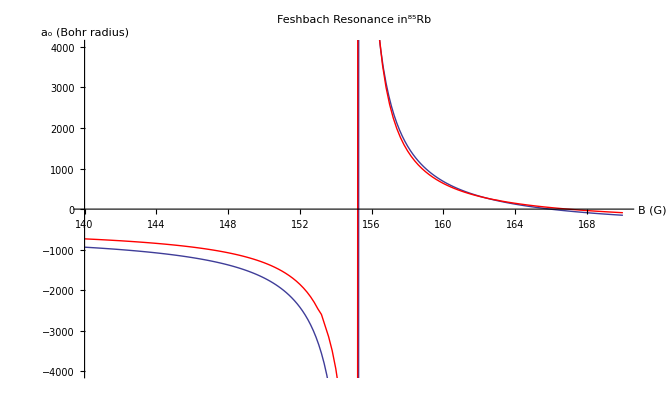

```mathematica
Mine=ListPlot[ScatList,AxesOrigin->{140,0},PlotRange->All,Joined->True(*,PlotStyle->Dashed*)];

Gr1=Show[Mine,Jose,PlotRange->{{140,170},{-4000,4000}},PlotLabel->"Feshbach Resonance in^85Rb",AxesLabel->{"B (G)","a_o (Bohr radius)"}]
```

```mathematica
Export["/home/cnewby/SeniorDesign/Final/YamaGraphRb.eps",Gr1]
```

/home/cnewby/SeniorDesign/Final/YamaGraphRb.eps

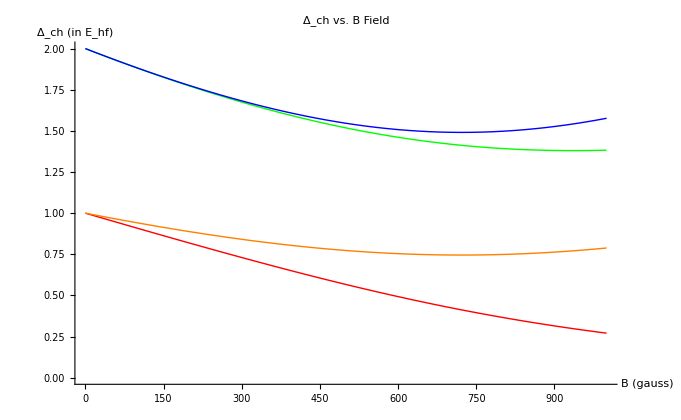

```mathematica
Ag=ListPlot[δalist,Joined->True,PlotStyle->Red];
Bg=ListPlot[δblist,Joined->True,PlotStyle->Orange];
Cg=ListPlot[δclist,Joined->True,PlotStyle->Green];
Dg=ListPlot[δdlist,Joined->True,PlotStyle->Blue];
Gr2=Show[{Ag,Bg,Cg,Dg},PlotRange->{{0,1000},{0,2}},PlotLabel->"Δ_ch vs. B Field",AxesLabel->{"B (gauss)","Δ_ch (in E_hf)"}]
```

```mathematica
Export["/home/cnewby/SeniorDesign/Final/DeltavsBfield.eps",Gr2]
```

/home/cnewby/SeniorDesign/Final/DeltavsBfield.eps